```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/yunqiguo/Document/EE232/proj2/src

```mathematica
<<actor.mx
```

```mathematica
actorMap=Flatten[Table[{#[[1]],t},{t,#[[2;;]]}]&/@actor,1];
```

```mathematica
actorMap=GroupBy[actorMap,Last->First];
```

```mathematica
movieActor=actorMap;
```

```mathematica
Length@actorMap
```

879201

```mathematica
actScore=Import["../data/actScore.txt","Data"][[All,2]];
```

```mathematica
actName=Import["../data/actRank.txt","Data"][[All,3;;4]];
```

```mathematica
actScore=Association@Table[actName[[i,1]]->actScore[[i]],{i,Length@actName}];
```

```mathematica
actMovieNumbers=Association@Table[actName[[i,1]]->actName[[i,2]],{i,Length@actName}];
```

```mathematica
topDirector=Import["../data/top_100_director.txt"]~StringSplit~"\n";
topDirector=Association@Table[topDirector[[i]]->i,{i,100}];
```

```mathematica
movieDirector=Import["../data/director_movies.txt","String"];
```

```mathematica
cleanData[str_]:=Module[{actors,cleanedActorData},
actors=StringSplit[str,"\n"];actors=Map[StringSplit[#,"\t\t"]&,actors];actors=Select[actors,Length[#]>4&];Return@Map[StringReplace[#, (StartOfString ~~Whitespace) | (Whitespace ~~ EndOfString) -> ""]&,actors,2]
]
```

```mathematica
movieDirector=cleanData@movieDirector;
```

```mathematica
movieDirector=Association@Flatten[Table[t->#[[1]],{t,#[[2;;]]}]&/@movieDirector,1];
```

```mathematica
movieList=Import["../data/newMovieList.txt","String"]~StringSplit~"\n"~StringSplit~"\t\t";
```

```mathematica
movieList[[All,3]]=ToExpression@movieList[[All,3]];
```

```mathematica
Sort[TakeLargest[actScore/@movieActor[movieList[[4,1]]],5]]
```

{5.98228×10^-6,7.20388×10^-6,0.0000102305,0.0000115492,0.0000253019}

```mathematica
directorRank[str_]:=Module[{tmp},
If[MissingQ[movieDirector[str]],Return@101];
tmp=topDirector[movieDirector[str]];
If[MissingQ[tmp],Return@101,Return@tmp]
]
```

```mathematica
selectSet=Select[movieList,Length@movieActor@#[[1]]≥5&];
```

```mathematica
Length@selectSet
```

96125

```mathematica
feature=Table[Join[ConstantArray[0,101],Sort[TakeLargest[actScore/@movieActor[selectSet[[i,1]]],5]],selectSet[[i]]]
,{i,Length@selectSet}];
Do[feature[[i,directorRank@selectSet[[i]] ]] = 1,{i,Length@selectSet}]
```

```mathematica
train=Select[feature,#[[-1]]≥0&];
```

```mathematica
test=Select[feature,#[[-1]]<0&];
```

```mathematica
train=RandomSample@train;
```

```mathematica
trainSplit=Partition[train,Floor@(Length@train/5)];
```

```mathematica
pm={};
Do[
Print@i;
training=Catenate[Drop[trainSplit,{i}]];
testing = trainSplit[[i]];
p=Predict[training[[All,1;;-4]]->training[[All,-1]],Method->"NeuralNetwork"];
testset=Table[t[[1;;-4]]->t[[-1]],{t,testing}];
tmp=PredictorMeasurements[p,testset];
Print[tmp["StandardDeviation"]];
AppendTo[pm,tmp],
(*{i,5}*)
{i,1}
]
```

1

1.26141

```mathematica
Export["../result/p8_f1_NN.pdf",pm[[1]]["ComparisonPlot"]]
```

../result/p8_f1_NN.pdf

```mathematica
sd=Table[pm[[i]]["StandardDeviation"],{i,5}];
```

```mathematica
Mean@sd
```

1.25891

```mathematica
StandardDeviation[train[[All,-1]]]
```

1.2646

```mathematica
Export["../result/p8_2.txt",Append[sd,Mean@sd]]
```

../result/p8_2.txt

use new feature

```mathematica
genreMovies=GroupBy[selectSet,#[[2]]&->First];
```

```mathematica
movieScore=Association@Table[t[[1]]->t[[3]],{t,selectSet}];
```

```mathematica
Keys@genreMovies
```

{Romance,Documentary,Comedy,Drama,Thriller,Music,Family,Horror,Western,Short,Fantasy,Sport,Sci-Fi,Action,Talk-Show,War,Musical,Crime,History,Mystery,News,Adventure,Biography,Film-Noir,Adult,Reality-TV,Animation,Game-Show}

```mathematica
genreScore=Association@Table[t->Mean[movieScore/@genreMovies[t]],{t,Keys@genreMovies}];
```

```mathematica
feature=Table[Join[{Length[actMovieNumbers/@movieActor[selectSet[[i,1]]]],Floor@Mean[actMovieNumbers/@movieActor[selectSet[[i,1]]]],genreScore[selectSet[[i,2]]]},selectSet[[i,{2,1,3}]]]
,{i,Length@selectSet}];
```

```mathematica
feature[[1]]
```

{11,26,6.09007,Romance,Suuri illusioni (1985),4.}

```mathematica
trainingFeature = {#[[1;;-4]],#[[-1]]}&/@feature[[All]];
```

```mathematica
train=Select[trainingFeature,#[[-1]]≥0&];
```

```mathematica
test=Select[trainingFeature,#[[-1]]<0&];
```

```mathematica
train=RandomSample@train;
```

```mathematica
trainSplit=Partition[train,Floor@(Length@train/5)];
```

```mathematica
pm={};
Do[
Print@i;
training=Catenate[Drop[trainSplit,{i}]];
testing = trainSplit[[i]];
p=Predict[training[[All,1]]->training[[All,2]],Method->"NeuralNetwork"];
testset=Table[t[[1]]->t[[2]],{t,testing}];
tmp=PredictorMeasurements[p,testset];
Print[tmp["StandardDeviation"]];
AppendTo[pm,tmp],
{i,5}
]
```

1

$Aborted

```mathematica
test[[1]]
```

{{92,16,5.16796},-1.}

```mathematica
p/@test[[All,1]]
```

{5.60854,6.21141,6.03506}

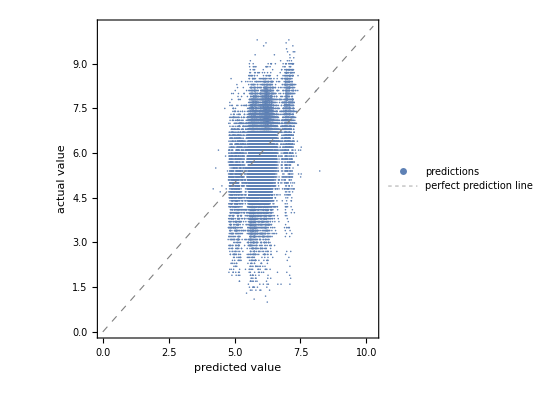

```mathematica
pm[[1]]["ComparisonPlot"]
```

```mathematica
Export["../result/p8_f5(number+penre)_Nearest.pdf",pm[[1]]["ComparisonPlot"]]
```

../result/p8_f5(number+penre)_Nearest.pdf

```mathematica
sd=Table[pm[[i]]["StandardDeviation"],{i,5}];
```

```mathematica
Mean@sd
```

1.18263

```mathematica
StandardDeviation[train[[All,-1]]]
```

1.2646

```mathematica
p
```

PredictorFunction[…]

```mathematica
Export["../result/p8_2.txt",Append[sd,Mean@sd]]
```

../result/p8_2.txt